```mathematica
Exit[]
```

```mathematica
DSolve[f'[x]-r*f[x]-c==0,f[x],x]
```

{{f[x]→-c/r+ⅇ^(r x) C[1]}}

```mathematica
n=2000;dW=RandomReal[NormalDistribution[],{n}]/Sqrt[n];W=Join[{0},Table[Sum[dW[[i]],{i,1,t}],{t,1,n-1}]];
```

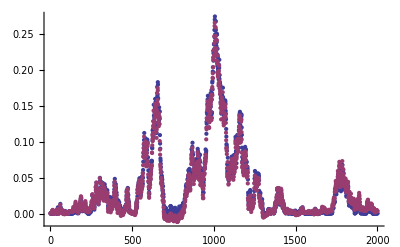

```mathematica
n=2000;dW=RandomReal[NormalDistribution[],{n}]/Sqrt[n];W=Join[{0},Table[Sum[dW[[i]],{i,1,t}],{t,1,n-1}]];
IWdW=Table[Sum[W[[i]]*dW[[i]],{i,1,t}]+t/2/n,{t,1,n}];
ListPlot[{W^2/2,IWdW}]
```

## Stop-Loss Start-Gain

```mathematica
U={};
```

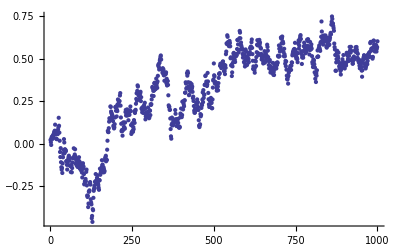

```mathematica
n=500000;dW=RandomReal[NormalDistribution[],{n}]/Sqrt[n];W=Accumulate[dW];ListPlot[Table[W[[i*500]],{i,1,n/500}]]
```

```mathematica
a=0.001;
IfsdW=Accumulate[dW*fs[W,a]];
IThetadW=Accumulate[dW*HeavisideTheta[W-0.2]];
L=Accumulate[fss[W,a]]/n;
```

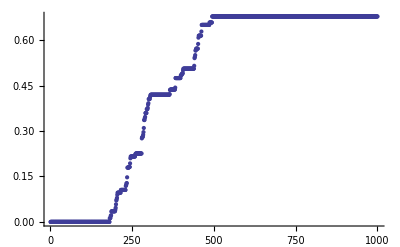

```mathematica
ListPlot[{str[IThetadW]-(Max[0,#-0.2]&/@str[W])}]
```

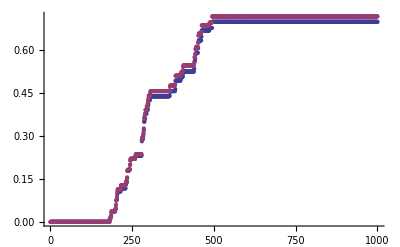

```mathematica
ListPlot[{str[IfsdW]-f[str[W],a],str[L]/2}]
```

```mathematica
fss[ft_,a_]:=(HeavisideTheta[ft-0.2+a]-HeavisideTheta[ft-0.2-a])/2/a;f[x_,b_]:=1/b HeavisideTheta[x] ((-0.010000000000000002-0.25 b (0.4+b)+0.1 x+0.5 b x-0.25 x^2) HeavisideTheta[-0.2-b+x]+(0.010000000000000002+0.25 (-0.4+b) b-0.1 x+0.5 b x+0.25 x^2) HeavisideTheta[-0.2+b+x]);fs[x_,b_]:=1/b HeavisideTheta[x] (-0.5 (-0.2-1. b+x) HeavisideTheta[-0.2-b+x]+0.5 (-0.2+b+x) HeavisideTheta[-0.2+b+x])
```

```mathematica
str[x_]:=Table[x[[i*n/1000]],{i,1,1000}]
```

```mathematica
+
```